## Лабораторная работа 4 Робилко Тимур, гр . 221701, Вариант 10

### Задание 1

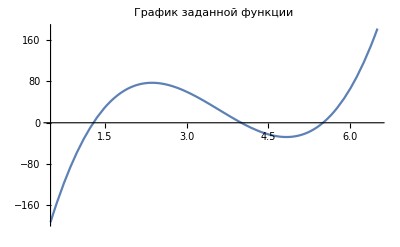

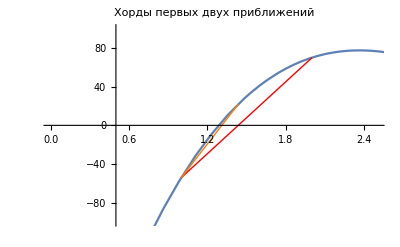

Найденный корень: 1.286; Число итераций: 5

```mathematica
f[x_] := 14 x^3-151 x^2+479x-396;

initialPlot = Plot[f[x], {x, 0.5,6.5}, PlotLabel -> "График заданной функции"];
ϵ = 10^-3;
a = 1;
b = 2;

ChordMethod[f_,a_,b_,eps_]:=Module[{x0=a,x1=b,x2,n=0},While[Abs[f[x1]]>eps&&Abs[x1-x0]>eps,x2=x1-f[x1] (x1-x0)/(f[x1]-f[x0]);
x0=x1;
x1=x2;
n++;];
{x1,n}];

{root,iterations}=ChordMethod[f,a,b,ϵ];

firstApproximation=Line[{{a,f[a]},{b,f[b]}}];
secondApproximationX=b-f[b] (b-a)/(f[b]-f[a]);
secondApproximation=Line[{{a,f[a]},{secondApproximationX,f[secondApproximationX]}}];

Show[initialPlot]
Show[initialPlot,Graphics[{Red,firstApproximation, Orange,secondApproximation}],PlotRange->{{0,2.5},{-100,100}},PlotLabel->"Хорды первых двух приближений"]

Print["Найденный корень: ", N[root, 4], "; Число итераций: ", iterations];
```

### Задание 2

```mathematica
Clear[f];
f = x^6-x^5-19 x^4-15 x^3+46 x^2+28x-40;

Print["Корни Solve: ", N[Solve[f == 0, x], 1]]
Print["Корни NSolve: ", N[NSolve[f == 0, x], 1]]
Print["Корни Roots: ", N[Roots[f == 0,x], 1]]
Print["Корень FindRoot: ", N[FindRoot[f == 0, {x,0}], 1]]
Print["Разложение: ", Factor[f]]
```

Корни Solve: {{x→-2.},{x→-2.},{x→-2.},{x→1.},{x→1.},{x→5.}}

Корни NSolve: {{x→-2.},{x→-2.},{x→-2.},{x→1.},{x→1.},{x→5.}}

Корни Roots: x==-2.||x==-2.||x==-2.||x==1.||x==1.||x==5.

Корень FindRoot: {x→1.}

Разложение: (-5+x) (-1+x)^2 (2+x)^3

### Задание 3

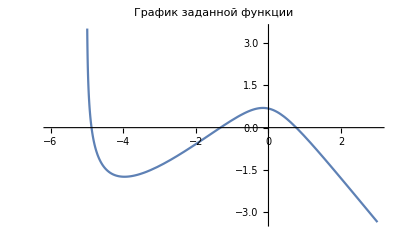

Решение x=0.764576 получено методом Ньютона на 3 итерации.

Решение x=0.764562 получено методом Секущих на 2 итерации.

```mathematica
Clear[f];
f[x_] := 4-√(2 x^2+1)-Log[2,x+5];

initialPlot = Plot[f[x], {x,-6,3}, PlotLabel->"График заданной функции"];
Show[initialPlot]

(* Метод Ньютона *)
ϵ = 10^-3;
maxIterations=50;
x1 = 1; (* Начальное приближение *)

Do[x2 = x1;
x1 = (x1 - f[x1]/f'[x1]) //N;
If[Abs[x2-x1]<ϵ,
Print["Решение x=", x2 // N, " получено методом Ньютона на ", n , " итерации."];
Break[]],
{n,1,maxIterations}]

(* Метод Секущих *)
ϵ = 10^-3;
maxIterations=50;
x1 = 1; (* Начальное приближение *)

Do[x3 = x2; x2 = x1;
x1 = (x1 - f[x1]((x1-x3)/(f[x1]-f[x3]))) //N;
If[Abs[x2-x1]<ϵ,
Print["Решение x=", x2 // N, " получено методом Секущих на ", n , " итерации."];
Break[]],
{n,1,maxIterations}]
```

### Задание 4

```mathematica
φ[x_] = 2^(4-√(2 x^2+1))-5
```

```mathematica
ϵ = 10^-3;
maxIterations=50;
x1 = -5; (* Начальное приближение *)

Do[x2 = x1;
x1 = φ[x1] //N;
If[Abs[x2-x1]<ϵ,
Print["Решение x=", x2 // N, " получено методом простой итерации на ", n , " итерации."];
Break[]],
{n,1,maxIterations}]
```

Решение x=-4.87187 получено методом простой итерации на 4 итерации.

### Задание 5

```mathematica
solveRoots = Solve[f[x] == 0, x];
nSolveRoots = NSolve[f[x] == 0, x];
findRootRoots = FindRoot[f[x] == 0, {x,0}];

Print["Уравнение решается только с помощью функции FindRoot: ", N[findRootRoots, 4]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

Уравнение решается только с помощью функции FindRoot: {x→0.764561}

### Задание 6

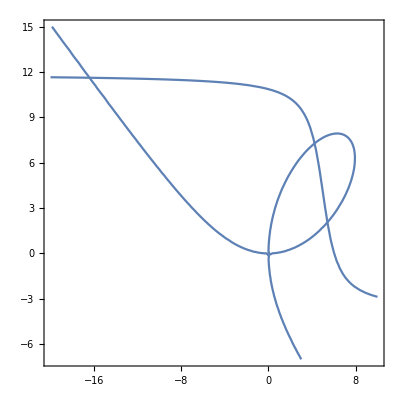

{x→-16.4269,y→11.6208}

{x→4.22911,y→7.28367}

{x→5.40918,y→2.05805}

```mathematica
Clear[f];
f[x_, y_] = x^3+y^3-15x*y;
g[x_,y_] = y-4+5ArcTan[x-5];

graph1 = ContourPlot[f[x,y] == 0, {x, -20,10}, {y,-7,15}];
graph2 = ContourPlot[g[x,y] == 0, {x, -20,10}, {y,-7,15}];
Show[graph1, graph2]

FindRoot[{f[x,y] == 0, g[x,y] == 0}, {x,-17}, {y,10}]
FindRoot[{f[x,y] == 0, g[x,y] == 0}, {x,3}, {y,5}]
FindRoot[{f[x,y] == 0, g[x,y] == 0}, {x,5}, {y,1}]
```